```mathematica
SetDirectory[NotebookDirectory[]]
```

S:\Research\WorkSpace\OrderTest\Correlation Stuff\New folder\NucComp\Eta50 Samples\NewTest\Clean Room\FFTWIntegrationAttempt\New folder

```mathematica
(*These comments are added later than actual cosntruction of the inputs, minor discrepencies may exist*)

(*PRIDE: Input is a single point at index 1 (not zero) with magnitude 10*)
(*Last version has this undego a single, BACKWARD transformation*)
(*I suspect the actual data file was created with a FORWARD transformation*)
Pride=ReadList["Pride.txt",Number];
PrideIm=ReadList["PrideIm.txt",Number];
For[i=1,i≤Dimensions[Pride][[1]],i++,
Pride[[i]]={i,Pride[[i]]};
PrideIm[[i]]={i,PrideIm[[i]]};
]

(*GREED: Input is a single point at index 2 with magnitude 10*)
(*Last version has this undergo a single, FORWARD transformation*)
Greed=ReadList["Greed.txt",Number];
GreedIm=ReadList["GreedIm.txt",Number];
For[i=1,i≤Dimensions[Greed][[1]],i++,
Greed[[i]]={i,Greed[[i]]};
GreedIm[[i]]={i,GreedIm[[i]]};
]

(*SLOTH: Input is a single point at index 62 with magnitude 10*)
(*Last version has this undergo a single, FORWARD transformation*)
(*62 is the central value of the array size 125*)
Sloth=ReadList["Sloth.txt",Number];
SlothIm=ReadList["SlothIm.txt",Number];
For[i=1,i≤Dimensions[Sloth][[1]],i++,
Sloth[[i]]={i,Sloth[[i]]};
SlothIm[[i]]={i,SlothIm[[i]]};
]

(*ENVY: Input is a single point at index 123 with magnitude 10*)
(*Last version has this undego a single, FORWARD transformation*)
Envy=ReadList["Envy.txt",Number];
EnvyIm=ReadList["EnvyIm.txt",Number];
For[i=1,i≤Dimensions[Envy][[1]],i++,
Envy[[i]]={i,Envy[[i]]};
EnvyIm[[i]]={i,EnvyIm[[i]]};
]

(*LUST: Input is a single point at index 100 with magnitude 5*)
(*Last version has this undego a FORWARD transformation, and then a BACKWARD transformation*)
Lust=ReadList["Lust.txt",Number];
LustIm=ReadList["LustIm.txt",Number];
For[i=1,i≤Dimensions[Lust][[1]],i++,
Lust[[i]]={i,Lust[[i]]};
LustIm[[i]]={i,LustIm[[i]]};
]

(*WRATH: Input is a single point at index 62 with magnitude 10*)
(*Last version has this undego a single, FORWARD transformation*)
(*WRATH compares to both SLOTH and ENVY because it uses N=63, hence it is the same index number as SLOTH, but same concept at ENVY*)
Wrath=ReadList["Wrath.txt",Number];
WrathIm=ReadList["WrathIm.txt",Number];
For[i=1,i≤Dimensions[Wrath][[1]],i++,
Wrath[[i]]={i,Wrath[[i]]};
WrathIm[[i]]={i,WrathIm[[i]]};
]

(*GREED: Input is a single point at index 5,0 with magnitude 10*)
(*Last version has this undergo a single, FORWARD transformation, but GLUTTONY is 2D*)
Gluttony=Import["Gluttony.txt","Table"];
GluttonyIm=Import["GluttonyIm.txt","Table"];
GluttonyIn=Import["GluttonyIn.txt","Table"];
```

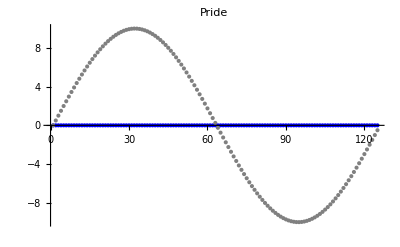

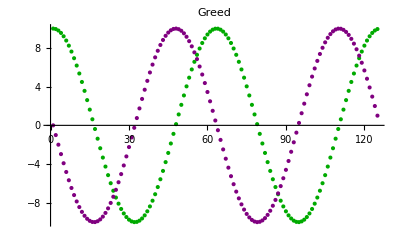

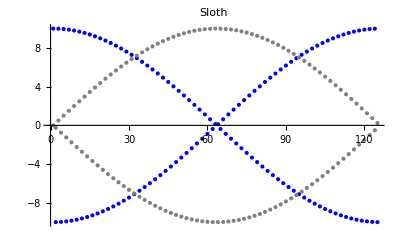

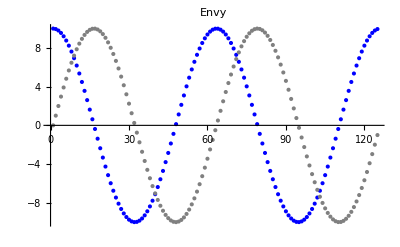

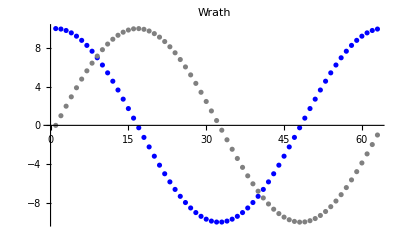

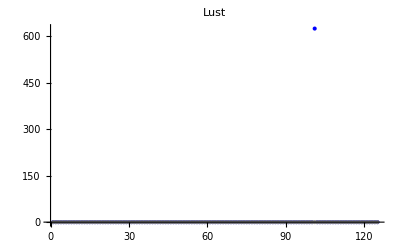

-Graphics3D-

-Graphics3D-

```mathematica
PridePlot=ListPlot[{Pride,PrideIm},PlotStyle->{Blue,Gray},PlotLabel->"Pride"]
GreedPlot=ListPlot[{Greed,GreedIm},PlotStyle->{Darker[Green],Purple},PlotLabel->"Greed"]
SlothPlot=ListPlot[{Sloth,SlothIm},PlotStyle->{Blue,Gray},PlotLabel->"Sloth"]
EnvyPlot=ListPlot[{Envy,EnvyIm},PlotStyle->{Blue,Gray},PlotLabel->"Envy"]
WrathPlot=ListPlot[{Wrath,WrathIm},PlotStyle->{Blue,Gray},PlotLabel->"Wrath"]
LustPlot=ListPlot[{Lust,LustIm},PlotStyle->{Blue,Gray},PlotLabel->"Lust"]
GluttonyPlot=ListPlot3D[{Gluttony,GluttonyIm}]
GluttonyPlot=ListPlot3D[GluttonyIn]
```

```mathematica
Lust[[101]]
```

{101,1250}

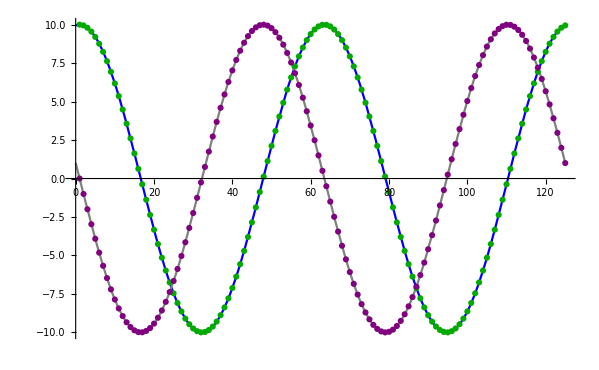

```mathematica
k=2*Pi/125;
n=2;
Analytics=Plot[{10*Cos[n*k*(x-1)],-10*Sin[n*k*(x-1)]},{x,0,125},PlotStyle->{Blue,Gray}];
Show[Analytics,GreedPlot]
```

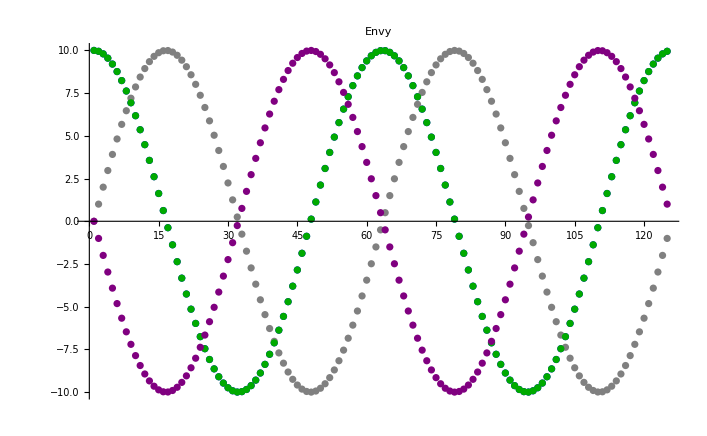

```mathematica
Show[EnvyPlot,GreedPlot]
```

```mathematica
GluttonyPlot=ListPlot3D[{Gluttony,GluttonyIm}]
GluttonyPlot=ListPlot3D[GluttonyIn]
```

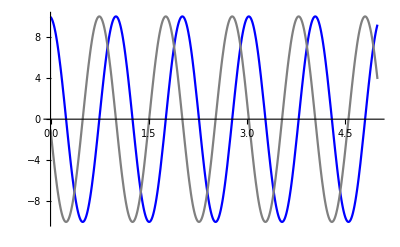

```mathematica
k=2*Pi/125;
n=123;
Analytics=Plot[{10*Cos[n*k*(x-1)],-10*Sin[n*k*(x-1)]},{x,0,5},PlotStyle->{Blue,Gray}]
```

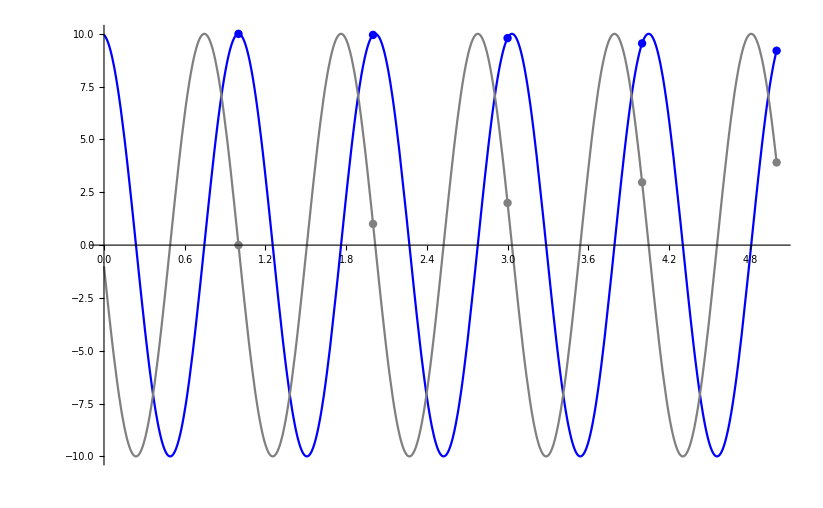

```mathematica
Show[Analytics,EnvyPlot]
```

```mathematica
Integrate[Exp[-p^2/(g*u)],p]
```

1/2 √g √π √u Erf[p/(√g √u)]

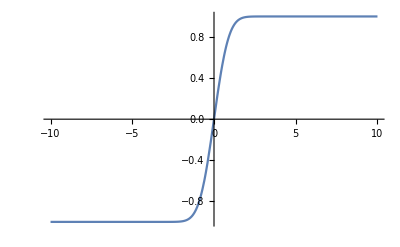

```mathematica
Plot[Erf[x],{x,-10,10}]
```

```mathematica
20*Pi/4.
```

15.708